```mathematica
f[x_,y_]:=If[(x<0.5)&&(x>0),Return[{2x,y/2}],Return[{2-2x,1-y/2}]]
```

```mathematica
init=Table[{RandomReal[],0.5*RandomReal[]},1];
```

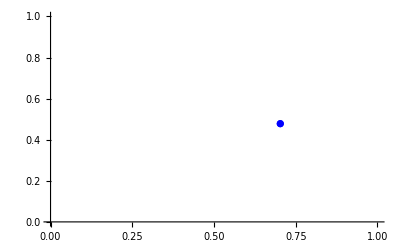

```mathematica
ListPlot[init,PlotRange->{{0,1},{0,1}},PlotStyle->Blue]
```

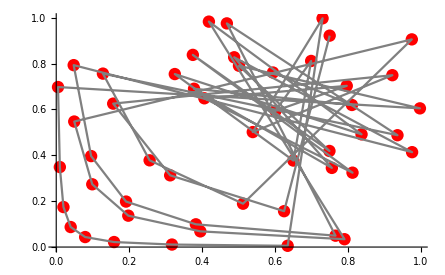

```mathematica
data=init;
p=Partition[Table[{
data=Table[f[data[[i]][[1]],data[[i]][[2]]],{i,1,Length[init]}];
data
},50]//Flatten,2];
ListPlot[p,PlotStyle->{Red,PointSize[0.02]}]~Show~ListLinePlot[p,PlotRange->{{0,1},{0,1}},PlotStyle->Gray]
```

```mathematica
|
```

```mathematica
data
```

{{0.75,0.921832}}

```mathematica
o
```

o